# #1: Emission Spectra and the Balmer Series of Hydrogen Josephine Brozny

```mathematica
{}
```

```mathematica
{}
```

## Abstract/Introduction

The purpose of the Emission Spectra and Balmer Series of Hydrogen is to find plank’s constant using the emission spectra from the balmer series of Hydrogen. Through a spectrometer we observed Mercury, Hydrogen, and Helium’s emission spectra. We did this by aligning the spectrometer and the prism in such a way where we could observe the lines of color in the eye piece. After lining up the crosshairs with the emission lines we were able to take the angular measurement of the spectrometer to find decimal angular measurement for each element and used Hydrogens to calculate plank’s constant. The angular measurements of Hydrogen at unknown wavelengths were 220.08 degrees, 215.08 degrees, and 211.33 degrees with an average value of 7.95 x 10^-32 (J/s) for plank’s constant. It does not agree with the accepted value which is 6.23 x 10^-34 (J/s) because of possible human errors. This may include inconsistencies and/or errors in reading angular measurements, lining the crosshairs, wavelength, lining the entire spectrometer, and the crack in our prism.

## Description of Experimental Procedure

Sketch of experimental setup is in scanned notebook pages. Spectrometers are used to take in light and break it into it’s spectral components. It does so by taking in light from a bright source through a slit in the collimator tube. By using a magnifying class in between the light source and collimator tube we are able to direct and amplify the light making it easier to see through the telescope. We are able to see light rays that are parallel to the collimator tube’s axis. The prism has an index of refraction related to wavelength which allows it to refract light at different angles which are what we measure. 

To begin this experiment we aligned and focused the spectrometer which was facing the Mercury lamp. We turned the lamp on, took a minute to position the magnifying lense while looking through the telescope the sharpen the image, and then continued to turn the prism. When we were able to see lines of color which represented the emission lines of Mercury, we matched the crosshairs on top of them and recorded their angular measurement. We did this for every emission line of every element.

## Results

### Part I: Measurements Performed

While observing Mercury’s spectrum we were able to find 7 visible colors with the exception of 4078 Violet (15). The readings of the angular measurements can be found on the scanned lab notebook. While observing Helium we were able to find 9 visible colors including a third yellow line of unknown wavelength with a measurement of 218.78 degrees. This line was not included in the given tables and figures. For Hydrogen we were only able to find 3 of the 4 angular measurements, recording angles of 220.08 degrees (red), 215.08 degrees (teal), and 211.33 degrees (purple). We converted the degrees into wavelength by dividing each quantity by 2pi and then taking the average of the 3 values to incorporate in our equation for plank’s constant, as seen on the scanned notebook pages. Our estimated value for plank’s constant is 7.95 x 10^-32 (J/s).

#### Data input

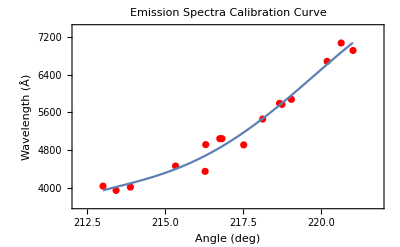

```mathematica
a={218.67, 218.75, 218.13, 213, 216.28, 217.52, 221.03, 220.65, 220.20, 219.05, 216.75, 216.30, 215.33, 216.82, 213.88, 213.42}; 
b={5791, 5770, 5461, 4047, 4358, 4916, 6907, 7065, 6678, 5876, 5048, 4922, 4471, 5048, 4026, 3956};
c={220.08, 215.08, 211.33};

d=Thread[{a,b}];
quartic=Fit[d,{1,x,x^2,x^3,x^4},x];
Show[ListPlot[d,PlotRange->{MinMax[a,Scaled[.1]],MinMax[b,Scaled[.1]]},PlotStyle->Red,Frame->True,Axes->False,FrameLabel->{"Angle (deg)","Wavelength (Å)"},PlotLabel->"Emission Spectra Calibration Curve"],Plot[{quartic},{x,Min[a],Max[a]}]]
f[x_]=quartic;
```

Balmer series wavelengths (Å)
f[c]
{6547.11,4345.25,3583.25}

#### Calculations: Systematic uncertainty. Here we take the root-mean-square of the deviations of data from the fit line and divide by √(N-5)(the 5 is because our 5-parameter fit reduces the number of degrees of freedom by 5). This is used to estimate systematic uncertainty of each wavelength above. The units are also Å.

```mathematica
√(Mean[(f[a]-b)^2]/(Length[a]-5))
```

47.4729

## Discussion

This is not within our estimated uncertainty of 0.01. Our calculated value for plank’s constant is 7.95 x 10^-32 (J/s) while the actual value is 6.23 x 10^-34 (J/s). For our set up, the most prominent systematic uncertainty was due to our prism being cracked through an entire corner which prevented us from seeing potential spectral lines. We were also not able to find every wavelength of light because our environment was not completely dark. There were people coming in and out of the blinds in our section and we couldn’t always get the black cloth to cover the set up completely which affected the already very sensitive spectrometer. As for human errors, we could have misaligned the prism, mirror, or spectrometer by either moving/tilting the objects or having them too close/far away. We calculated the 0.01 value for uncertainty by using the uncertainty of the vernier scale which is 0.01. Because each measurement shared the same value, the final uncertainty remained the same.

## Conclusion

In conclusion, we were not quite able to calculate plank’s constant exactly to 6.23 x 10^-34 (J/s), but we came relatively close with our calculation of 7.95 x 10^-32 (J/s). Many factors contributed to our uncertainty, including systematic and human errors. Even though we calculated plank’s constant through our own data and observations using the Balmer series of Hydrogen, we still did not obtain the correct value even within the 0.01 uncertainty range.

## Scanned Sheets from Lab Notebook